```mathematica
(* Initialisation *)
(* Evaluate before starting writing "real code" *)
(* Usage e.g.: "ld [Spacekey]" becomes "⊨", so writing "a ld 5" turns into "a⊨5" *) 
SetOptions[EvaluationNotebook[], 
			 InputAutoReplacements -> { (* special AceGen assignment operators: *) "ld"-> "⊨","ls"->"⊢","rd"->"⫤","rs"->"⊣",
					                                 (* brackets and symbols: *) "dbl"->"⟦","dbr"->"⟧","lcb"->"{","rcb"->"}","lsb"->"[","rsb"->"]","->"->"→",
					                                 (* shortcuts for starting/ending a comment block: *) "co"->"(*","cc"->"*)"
					                              }
		   ]
(* Output the current time, so we know when AceGen has been executed the last time *)
Now
```

Wed 29 May 2024 14:40:37GMT+2

```mathematica
(* Clear all old variables initially to have a fresh start *)
ClearAll["Global`*"] 
(* Start AceGen *) 
<<AceGen`;
Needs["AceTensorFunctions`"]; 

NAME = "SMSDo_Loops";
SMSInitialize[NAME,"Language"-> "Matlab","Mode"-> "Optimal"]; 

(* Define the maximum number of Newton-Raphson iterations, as this also defines the size of convergenceHistory$$ *) 
n iterations = 20;

(* Start a module, which represents the to be created function, with name "NAME" and the specified input and output arguments *) 
SMSModule[NAME,Real[ displacement$$, parameter$$, convergedValue$$, convergenceHistory$$[2,n iterations] ],
		"Input"-> { displacement$$, parameter$$ },
		"Output" -> { convergedValue$$, convergenceHistory$$ }
	       ];
displacement ⊨ SMSReal[ displacement$$ ];
parameter ⊨ SMSReal[ parameter$$ ];
```

Get::noopen: Cannot open AceTensorFunctions`.

Needs::nocont: Context AceTensorFunctions` was not created when Needs was evaluated.

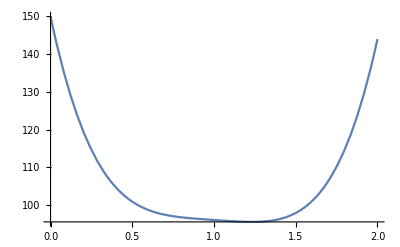

```mathematica
(* Define some energy function and plot it with an exemplary parameter=1 *) 
W energy[utmp_,parameter_]:=( 1/2 * 100 * (utmp-parameter)^4+utmp^2 -5utmp+100);
Plot[W energy[x,1],{x,0,2}]
```

```mathematica
(* #1 Works: *) 
u tmp ⫤ displacement;
SMSDo[i NR,1,n iterations,1,{u tmp}];
         (* Compute the energy to be minimised using the variable u tmp *) 
	W ⊨ W energy[u tmp,parameter];
         (* Find the mininum of the energy W by computing the slope of the energy which will be iteratively computed to find the minimum (R=0) *) 
	R ⊨ SMSD[W,u tmp];
         (* Give some output on the progress and export it to convergenceHistory$$ *) 
         SMSPrintMessage["iteration i_NR=",i NR,": W=",W,"; R=",R, "; SMSAbs[R]=",SMSAbs[R]];
         SMSExport[u tmp,convergenceHistory$$[i NR,1]];
         SMSExport[SMSAbs[R],convergenceHistory$$[i NR,2]];
         (* Check the residual for convergence *) 
	SMSIf[ SMSAbs[R]<1*^-8 ];
                  (* If converged, export the current value of u tmp *) 
		SMSExport[u tmp,convergedValue$$];
		SMSPrintMessage["converged"];
                  (* Leave the SMSDo-Loop *) 
		SMSBreak[];
	SMSEndIf[];
          (* If the maximum number of Newton-Raphson iterations is reached, we output the current value and report a convergence failure *) 
          SMSIf[ i NR >=n iterations];
		SMSExport[u tmp,convergedValue$$];
		SMSPrintMessage["failed"];
		SMSBreak[];
          SMSEndIf[];
          (* Compute the derivative and update the value of u tmp *) 
	dRdu ⊨ SMSD[R, u tmp];
	u tmp  ⊣ u tmp - 1/dRdu * R;
SMSEndDo[];
```

```mathematica
(* #2 Works: Without auxiliary variable "u tmp"
SMSDo[i NR,1,n iterations,1,{displacement}];
         (* Compute the energy to be minimised using the variable u tmp *) 
	W ⊨ W energy[displacement,parameter];
         (* Find the mininum of the energy W by computing the slope of the energy which will be iteratively computed to find the minimum (R=0) *) 
	R ⊨ SMSD[W,displacement];
         (* Give some output on the progress and export it to convergenceHistory$$ *) 
         SMSPrintMessage["iteration i_NR=",i NR,": W=",W,"; R=",R, "; SMSAbs[R]=",SMSAbs[R]];
         SMSExport[displacement,convergenceHistory$$[i NR,1]];
         SMSExport[SMSAbs[R],convergenceHistory$$[i NR,2]];
         (* Check the residual for convergence *) 
	SMSIf[ SMSAbs[R]<1*^-8 ];
                  (* If converged, export the current value of u tmp *) 
		SMSExport[displacement,convergedValue$$];
		SMSPrintMessage["converged"];
                  (* Leave the SMSDo-Loop *) 
		SMSBreak[];
	SMSEndIf[];
          (* If the maximum number of Newton-Raphson iterations is reached, we output the current value and report a convergence failure *) 
          SMSIf[ i NR >=n iterations];
		SMSExport[displacement,convergedValue$$];
		SMSPrintMessage["failed"];
		SMSBreak[];
          SMSEndIf[];
          (* Compute the derivative and update the value of u tmp *) 
	dRdu ⊨ SMSD[R, displacement];
	displacement ⊣ displacement - 1/dRdu * R;
SMSEndDo[];
*)
```

```mathematica
(* #3 Wrong. Value of "displacement" does not change. Use of multi-valued variable necessary.
SMSDo[i NR,1,n iterations,1,displacement];
	W ⊨ W energy[displacement,parameter];
	R ⊨ SMSD[W,displacement];
      (* Give some output on the progress and export it to convergenceHistory$$ *) 
         SMSPrintMessage["iteration i_NR=",i NR,": W=",W,"; R=",R, "; SMSAbs[R]=",SMSAbs[R]];
         SMSExport[displacement,convergenceHistory$$[i NR,1]];
         SMSExport[SMSAbs[R],convergenceHistory$$[i NR,2]];
         (* Check the residual for convergence *) 
	SMSIf[ SMSAbs[R]<1*^-8 ];
		SMSExport[displacement,convergedValue$$];
		SMSPrintMessage["converged"];
		SMSBreak[];
	SMSEndIf[];
          (* If the maximum number of Newton-Raphson iterations is reached, we output the current value and report a convergence failure *) 
          SMSIf[ i NR >=n iterations];
		SMSExport[displacement,convergedValue$$];
		SMSPrintMessage["failed"];
		SMSBreak[];
          SMSEndIf[];
	dRdu ⊨ SMSD[R, displacement];
	displacement ⊢ displacement - 1/dRdu * R; (* "⊢" wrong, use "⊣" instead *) 
SMSEndDo[];  *)
```

```mathematica
(* #4 Works. Value of "displacement" is sent out of the loop. 
SMSDo[i NR,1,n iterations,1,displacement];
	W ⊨ W energy[displacement,parameter];
	R ⊨ SMSD[W,displacement];
      (* Give some output on the progress and export it to convergenceHistory$$ *) 
         SMSPrintMessage["iteration i_NR=",i NR,": W=",W,"; R=",R, "; SMSAbs[R]=",SMSAbs[R]];
         SMSExport[displacement,convergenceHistory$$[i NR,1]];
         SMSExport[SMSAbs[R],convergenceHistory$$[i NR,2]];
         (* Check the residual for convergence *) 
	SMSIf[ SMSAbs[R]<1*^-8 ];
		SMSPrintMessage["converged"];
		SMSBreak[];
	SMSEndIf[];
          (* If the maximum number of Newton-Raphson iterations is reached, we output the current value and report a convergence failure *) 
          SMSIf[ i NR >=n iterations];
		SMSPrintMessage["failed"];
		SMSBreak[];
          SMSEndIf[];
	dRdu ⊨ SMSD[R, displacement];
	displacement ⊣ displacement - 1/dRdu * R;
SMSEndDo[displacement]; (* necessary to set "displacement" as out_var *) 

SMSExport[displacement,convergedValue$$];
*)
```

```mathematica
(* @todo Add more cases and explanations as there are many ways to do it wrong here *)
```

```mathematica
(* Output the time at the end of the execution *)
Now 
(* Write output file containing all the above defined functions introduced by SMSModule *)
(* Create output file named "NAME", '"LocalAuxiliaryVariables" -> True' is a command to exclude the AceGen internal array "v" from the list of input and output arguments of the created subroutine *)
SMSWrite[NAME,"LocalAuxiliaryVariables" -> True]; 
(* Print the content of the just created file on screen (sensible only for small file sizes) *)
FilePrint[ StringJoin[NAME,Which[SMSLanguage=="Fortran",".f",
							   SMSLanguage=="Matlab",".m",
							   SMSLanguage=="C++",".cpp",
							   SMSLanguage=="C",".c"
							 ]
					]
		   ]
```

Wed 29 May 2024 14:40:37GMT+2

File: SMSDo_Loops.m  Size: 1963  Time: 1
Method | SMSDo_Loops
No.Formulae | 22
No.Leafs | 213

%**************************************************************
%* AceGen    7.505 Linux (16 Aug 22)                          *
%*           Co. J. Korelc  2020           29 May 24 14:40:38 *
%**************************************************************
% User     : Full professional version
% Notebook : AceGen-SMSDo
% Evaluation time                 : 1 s     Mode  : Optimal
% Number of formulae              : 22      Method: Automatic
% Subroutine                      : SMSDo_Loops size: 213
% Total size of Mathematica  code : 213 subexpressions
% Total size of Matlab code      : 1068 bytes 

%*********************** F U N C T I O N **************************
function[convergedValue,convergenceHistory]=SMSDo_Loops(displacement,parameter);
persistent v;
if size(v)<159
  v=zeros(159,'double');
end;
v(25)=0;
v(1)=displacement;
for i3=1:1:20;
 v(5)=-parameter+v(1);
 v(21)=(v(5)*v(5));
 v(33)=600e0*v(21);
 v(14)=2e0+v(33);
 v(6)=-5e0+2e0*v(1)+200e0*Power(v(5),3);
 v(34)=-600e0*(v(21)-(2e0*v(5)*v(6))/v(14));
 disp(sprintf("\n%s %f %s %f %s %f %s %f ","iteration i_NR=",i3,": W=",100e0-5e0*v(1)+(v(1)*v(1)) ...
  +50e0*Power(v(5),4),"; R=",v(6),"; SMSAbs[R]=",abs(v(6))));
 convergenceHistory(i3,1)=v(1);
 convergenceHistory(i3,2)=abs(v(6));
 if(i3>=20)
  disp(sprintf("\n%s ","failed"));
  break;
 else;
 end;
 v(25)=(v(25)*v(33)+(-1e0+v(25))*v(34))/v(14);
 v(1)=v(1)-v(6)/v(14);
 if(abs(v(6))<0.1e-7)
  disp(sprintf("\n%s ","converged"));
  v(18)=0;
  v(18)=(v(18)*v(33)+(-1e0+v(18))*v(34))/v(14);
  disp(sprintf("\n%s %f ","du/dparameter_in =",v(18)));
  break;
 else;
 end;
end;
disp(sprintf("\n%s %f ","du/dparameter_out=",v(25)));
convergedValue=v(1);


function [x]=SMSKDelta(i,j)

if (i==j) , x=1; else x=0; end;

end

function [x]=SMSDeltaPart(a,i,j,k)

l=round(i/j);

if (mod(i,j) ~= 0 | l>k) , x=0; else x=a(l); end;

end

function [x]=Power(a,b)

x=a^b;

end

function [x]=SMSTernaryOperator(a,b,c)

if (c) , x=a; else x=b; end;

end

end